## Plotting in Mathematica

## 2D plotting

### Basic plot

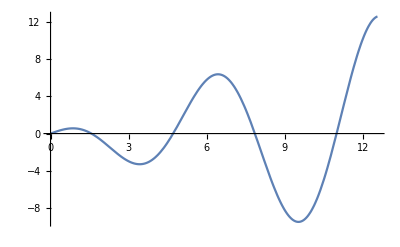

```mathematica
Plot[t*Cos[t],{t,0,4*π}]
```

#### Labels

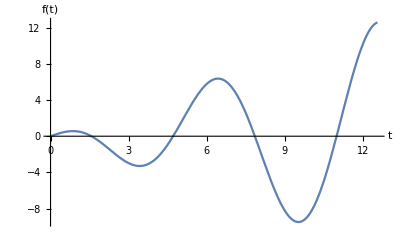

```mathematica
Plot[t*Cos[t],{t,0,4*π}, 
AxesLabel->{"t","f(t)"}]
```

#### Title

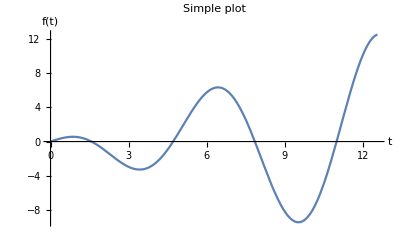

```mathematica
Plot[t*Cos[t],{t,0,4*π}, 
AxesLabel->{"t","f(t)"},
PlotLabel->"Simple plot"]
```

#### Grid Lines

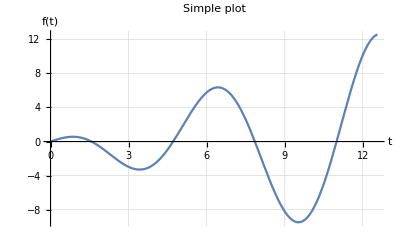

```mathematica
Plot[t*Cos[t],{t,0,4*π}, 
AxesLabel->{"t","f(t)"},
PlotLabel->"Simple plot",
GridLines->Automatic]
```

#### Change line styles

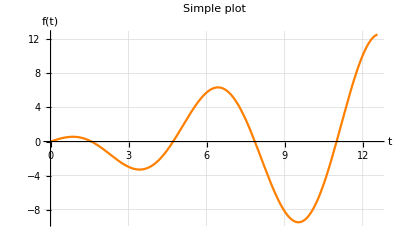

```mathematica
Plot[t*Cos[t],{t,0,4*π}, 
AxesLabel->{"t","f(t)"},
PlotLabel->"Simple plot",
GridLines->Automatic,
PlotStyle->Orange]
```

#### More line styles

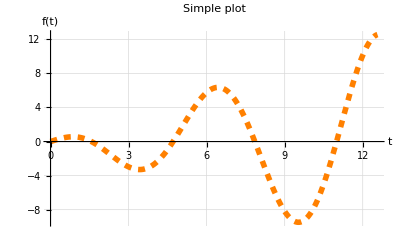

```mathematica
Plot[t*Cos[t],{t,0,4*π}, 
AxesLabel->{"t","f(t)"},
PlotLabel->"Simple plot",
GridLines->Automatic,
PlotStyle->{Orange,Dashed,Thickness[0.01]}]
```

#### Plot entire range

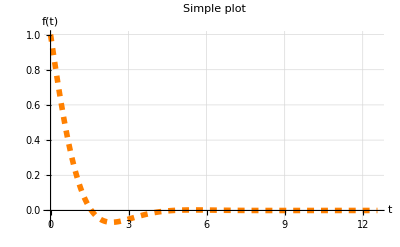

```mathematica
Plot[Exp[-t]*Cos[t],{t,0,4*π}, 
AxesLabel->{"t","f(t)"},
PlotLabel->"Simple plot",
GridLines->Automatic,
PlotStyle->{Orange,Dashed,Thickness[0.01]},
PlotRange->All]
```

## Multiple plots

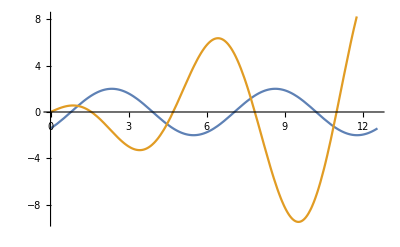

```mathematica
Plot[{2*Sin[t-π/4],t*Cos[t]},{t,0,4*π}]
```

#### Legends

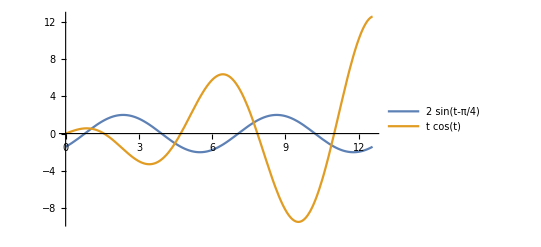

```mathematica
Plot[{2*Sin[t-π/4],t*Cos[t]},{t,0,4*π},
PlotRange->All,
PlotLegends->"Expressions"]
```

## Better way to overlay plot : The Show command

-Graphics-

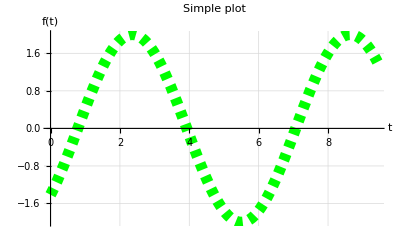

```mathematica
plot1=Plot[t*Cos[t],{t,0,4*π}, 
AxesLabel->{"t","f(t)"},
PlotLabel->"Simple plot",
GridLines->Automatic,
PlotStyle->{Orange,Dashed,Thickness[0.01]}]
plot2=Plot[2*Sin[t-π/4],{t,0,3*π}, 
AxesLabel->{"t","f(t)"},
PlotLabel->"Simple plot",
GridLines->Automatic,
PlotStyle->{Green,Dashed,Thickness[0.02]}]
```

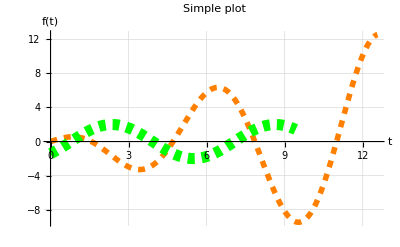

```mathematica
Show[plot1,plot2]
```

#### Plot options for Show

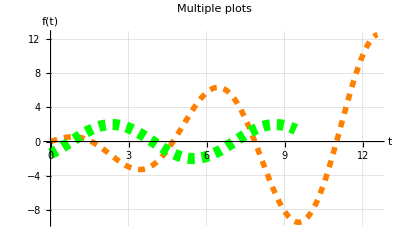

```mathematica
Show[plot1,plot2,
PlotLabel-> "Multiple plots",
AxesLabel-> {"t","f(t)"},
PlotRange-> All,
GridLines-> Automatic]
```

#### Legends for Show

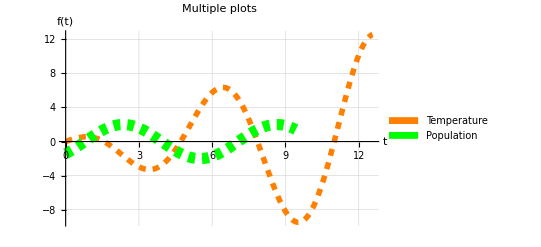

```mathematica
Legended[Show[plot1,plot2,
PlotLabel-> "Multiple plots",
AxesLabel-> {"t","f(t)"},
PlotRange-> All,
GridLines-> Automatic],
SwatchLegend[{Orange, Green},{"Temperature","Population"}]]
```

#### ListPlot

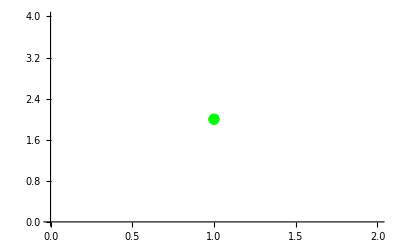

```mathematica
pt1={{1,2}}; (*Row Matrix*)
ListPlot[pt1,
PlotStyle->{Green,PointSize[0.02]}]
```

(1 | 2
4 | 5
7 | 8)

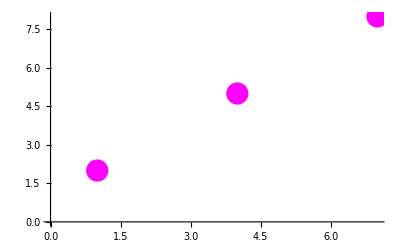

```mathematica
points={{1,2},{4,5},{7,8}};
points //MatrixForm
plotA=ListPlot[points,
PlotStyle->{Magenta,PointSize[0.04]}]
```

#### Connecting with lines

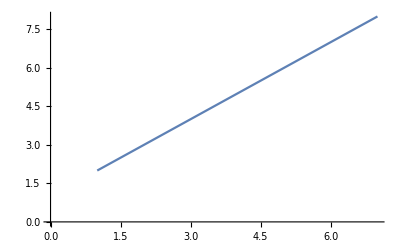

```mathematica
points={{1,2},{4,5},{7,8}};
PlotB=ListLinePlot[points,
PlotStyle->{Grey,PointSize[0.04]}]
```

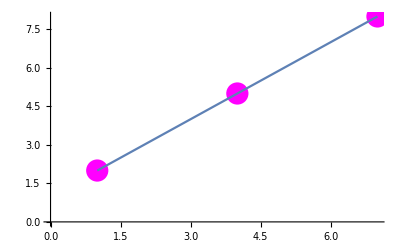

```mathematica
Show[plotA,PlotB]
```

#### Realistic plots

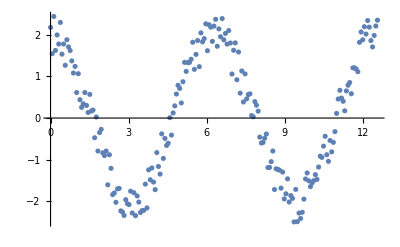

```mathematica
data=Table[{t,2 Cos[t]+RandomReal[]-0.5},{t,0,4*π,2 π/100}];
dataplot=ListPlot[data]
```

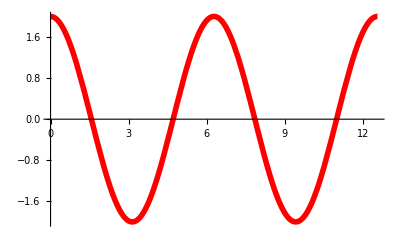

```mathematica
fitplot=Plot[2 Cos[t],{t,0,4*π},
PlotStyle->{Red, Thickness[0.01]}]
```

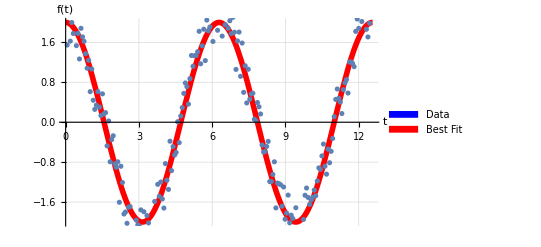

```mathematica
Legended[Show[fitplot,dataplot,
AxesLabel-> {"t","f(t)"},
GridLines-> Automatic],
SwatchLegend[{Blue,Red},{"Data","Best Fit"}]]
```

#### Discrete Plot

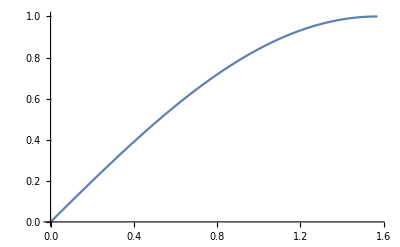

```mathematica
Plot[Sin[x],{x,0,π/2}]
```

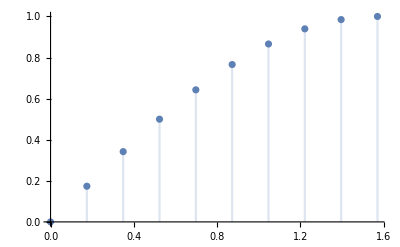

```mathematica
DiscretePlot[Sin[x],{x,0,π/2,10*π/180}]
```

#### Additional options

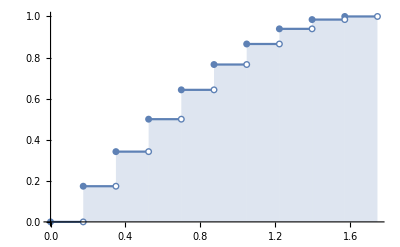

```mathematica
DiscretePlot[Sin[x],{x,0,π/2,10*π/180},
ExtentSize->Right,
ExtentMarkers->{"Filled","Empty"}]
```

#### Histogram

```mathematica
data2=Table[RandomReal[],{i,1,1000}];
```

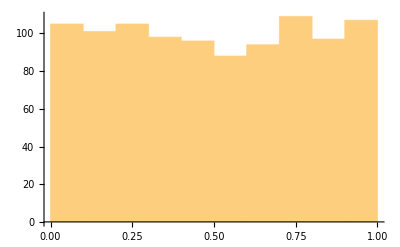

```mathematica
Histogram[data2]
```

#### PieChart

```mathematica
PieChart[{1,2,5}]
```

-Graphics-